```mathematica
ClearAll["Global`*"]
```

```mathematica
(* GAPDH Kinetics with 30 mM Tris, 10 mM Arsenate, pH 8.5 by MW-KK 2020 *)(* NAD+ levels are 0.125; 0.250, and 0.500 mM *)
cGAP={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800};
v125={0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188};
v250={0.050,0.104,0.150,0.182,0.237,0.241,0.264,0.259,0.266,0.232};
v500={0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.310,0.334,0.322};
```

```mathematica
cGAP={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800};
v125={0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188};
```

```mathematica
{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8}
```

{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8}

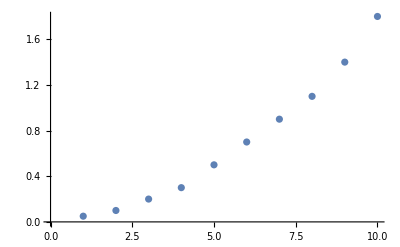

```mathematica
PlotA=ListPlot[{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8}]
```

```mathematica
cGAP={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800};
```

```mathematica
v250={0.050,0.104,0.150,0.182,0.237,0.241,0.264,0.259,0.266,0.232};
```

```mathematica
{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}
```

{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}

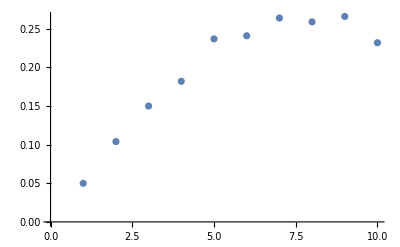

```mathematica
PlotB=ListPlot[{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}]
```

```mathematica
cGAP={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800};
```

```mathematica
v500={0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.310,0.334,0.322};
```

```mathematica
{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}
```

{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}

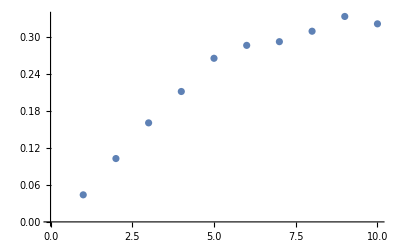

```mathematica
PlotC= ListPlot[{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}]
```

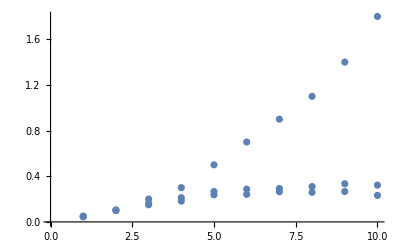

```mathematica
Show[PlotA, PlotB, PlotC]
```

```mathematica
(* Measured in absorbance units to reaction velocities 
by dividing the rate with the molar absorption coefficient of urate (ε340 = 6,220 cm-1 M-1).
You also need to invert the sign to positive because velocity is defined as 
v(t) = (-d[GAP])/d[t].
The spectrophotometer reports negative rates because it is determining the slope of the 
line, which is negative because of urate disappearance. *)
(* Experimental rate values (-AU/min) *)
Subscript[obsRate, data1]=QuantityArray[{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188},"per minute"]
Subscript[Α, data]={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800}
Subscript[ϵ, λ340]=Quantity[6220 ,1/("Centimeters"×"Molar")]
l=Quantity[1,"Centimeters"]
Subscript[ℂ, data1]=Subscript[Α, data]/(Subscript[ϵ, λ340]×l)
Subscript[ℂ, data1mmol]=UnitConvert[Subscript[ℂ, data1],"Millimolar"]
Subscript[rxnVel, data1]=Subscript[obsRate, data1]/(Subscript[ϵ, λ340]×l)
Subscript[rxnVel, data1mmol]=UnitConvert[Subscript[rxnVel, data1],("Millimolar")/("Minutes")]
```

QuantityArray[…]

{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8}

6220 /(cm M)

1 cm

{8.03859×10^-6 M,0.0000160772 M,0.0000321543 M,0.0000482315 M,0.0000803859 M,0.00011254 M,0.000144695 M,0.000176849 M,0.00022508 M,0.000289389 M}

{0.00803859 mM,0.0160772 mM,0.0321543 mM,0.0482315 mM,0.0803859 mM,0.11254 mM,0.144695 mM,0.176849 mM,0.22508 mM,0.289389 mM}

QuantityArray[…]

QuantityArray[…]

```mathematica
Subscript[MMKinetics, data1]=Transpose[{QuantityMagnitude[Subscript[ℂ, data1mmol]],QuantityMagnitude[Subscript[rxnVel, data1mmol]]}]
Subscript[nlmFit, data1]=NonlinearModelFit[Subscript[MMKinetics, data1],(Subscript[V, MAX]×S)/(Subscript[κ, M]+S),{Subscript[V, MAX],Subscript[κ, M]},S]
Subscript[eqnMM, data1]=Normal[Subscript[nlmFit, data1]]

(* Statistics of Fit *)
Print["Statistics of Fit"]
Print["R^2 = ",Subscript[nlmFit, data1]["RSquared"]]
Print["Adjusted R^2 = ",Subscript[nlmFit, data1]["AdjustedRSquared"]]
Subscript[nlmFit, data1]["ParameterTable"]
Subscript[nlmFit, data1]["ParameterConfidenceIntervalTable"]
Subscript[paramtest, data1]=Subscript[nlmFit, data1]["BestFitParameters"]
Subscript[nlmFit, data1]["BestFit"]
```

{{0.00803859,0.0062701},{0.0160772,0.0152733},{0.0321543,0.0207395},{0.0482315,0.027492},{0.0803859,0.0302251},{0.11254,0.0292605},{0.144695,0.0308682},{0.176849,0.033119},{0.22508,0.0300643},{0.289389,0.0302251}}

FittedModel[(0.035025 S)/(0.0207047+S)]

(0.035025 S)/(0.0207047+S)

Statistics of Fit

R^2 = 0.994268

Adjusted R^2 = 0.992835

| Estimate | Standard Error | t-Statistic | P-Value
V_MAX | 0.035025 | 0.00155654 | 22.5019 | 1.61048×10^-8
κ_M | 0.0207047 | 0.0041968 | 4.93344 | 0.00114447

| Estimate | Standard Error | Confidence Interval
V_MAX | 0.035025 | 0.00155654 | {0.0314356,0.0386144}
κ_M | 0.0207047 | 0.0041968 | {0.0110268,0.0303825}

{V_MAX→0.035025,κ_M→0.0207047}

(0.035025 S)/(0.0207047+S)

```mathematica
Print["V_max/κ_M = ",QuantityMagnitude[Subscript[V, MAX]/. Subscript[paramtest, data1]]/(Subscript[κ, M]/. Subscript[paramtest, data1])]
```

V_max/κ_M = 1.69165

V_max/κ_M = 1.69165

V_max/κ_M = 1.69165

«2 more identical outputs»

V_max/κ_M = 1.69065

V_max/κ_M = 1.69165

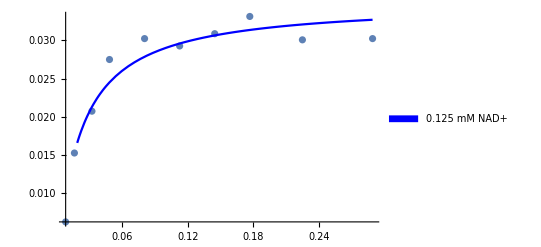

```mathematica
Part1A=Show[ListPlot[Subscript[MMKinetics, data1],PlotRange-> {{Min[QuantityMagnitude[Subscript[ℂ, data1mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data1mmol]]]},
{Min[QuantityMagnitude[Subscript[rxnVel, data1mmol]]],Max[QuantityMagnitude[Subscript[rxnVel, data1mmol]]]}}],Plot[Subscript[nlmFit, data1][S],{S,Min[QuantityMagnitude[Subscript[ℂ, data1mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data1mmol]]]},PlotStyle->{{Blue,PointSize[Medium]}},Frame->True,PlotLegends->SwatchLegend[{Blue}, {"0.125 mM NAD+"}],FrameLabel->Style["    Ping-Pong Mechanism"], AxesLabel->{ "[1/GAP],(1/mM","1/Vo,(min/AU)"},LabelStyle->Directive[14,Black]]]
```

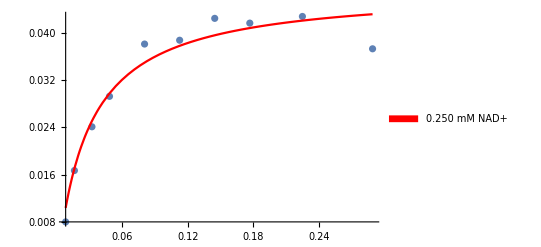

```mathematica
Part1B=Show[ListPlot[Subscript[MMKinetics, data2],PlotRange-> {{Min[QuantityMagnitude[Subscript[ℂ, data2mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data2mmol]]]},
{Min[QuantityMagnitude[Subscript[rxnVel, data2mmol]]],Max[QuantityMagnitude[Subscript[rxnVel, data2mmol]]]}}],Plot[Subscript[nlmFit, data2][S],{S,Min[QuantityMagnitude[Subscript[ℂ, data2mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data2mmol]]]},PlotStyle->{{Red,PointSize[Medium]}},Frame->True,PlotLegends->SwatchLegend[{Red}, {"0.250 mM NAD+"}],FrameLabel->Style["    Ping-Pong Mechanism"], AxesLabel->{ "[1/GAP],(1/mM","1/Vo,(min/AU)"},LabelStyle->Directive[14,Black]]]
```

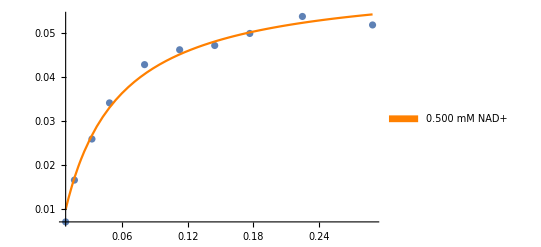

```mathematica
Part3A=Show[ListPlot[Subscript[MMKinetics, data3],PlotRange-> {{Min[QuantityMagnitude[Subscript[ℂ, data3mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data3mmol]]]},
{Min[QuantityMagnitude[Subscript[rxnVel, data3mmol]]],Max[QuantityMagnitude[Subscript[rxnVel, data3mmol]]]}}],Plot[Subscript[nlmFit, data3][S],{S,Min[QuantityMagnitude[Subscript[ℂ, data3mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data3mmol]]]},PlotStyle->{{Orange,PointSize[Medium]}},Frame->True,PlotLegends->SwatchLegend[{Orange}, {"0.500 mM NAD+"}],FrameLabel->Style["    Ping-Pong Mechanism"], AxesLabel->{ "[1/GAP],(1/mM","1/Vo,(min/AU)"},LabelStyle->Directive[14,Black]]]
```

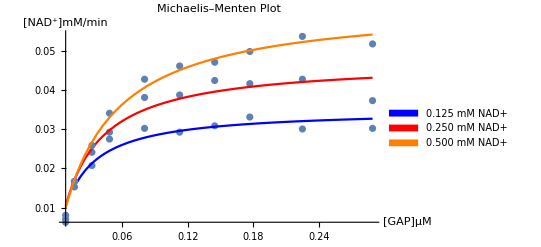

Kinetics_DATA1.png

```mathematica
PlotMM=Show[{Part1A,Part1B,Part3A}, PlotRange->All,PlotLabel->Style["    Michaelis–Menten Plot"],AxesLabel->{"[GAP]μM","[NAD^+]mM/min"},
LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0]}]
Export["Kinetics_DATA1.png",PlotMM]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Kinetics_DATA1.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Kinetics_DATA1.png"]]]
```

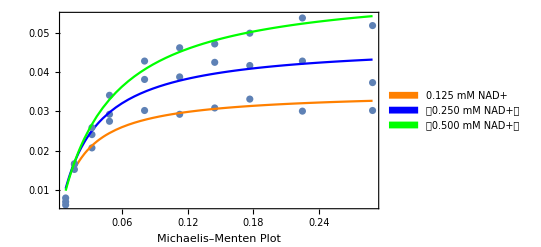

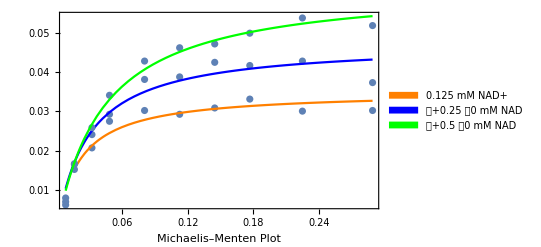

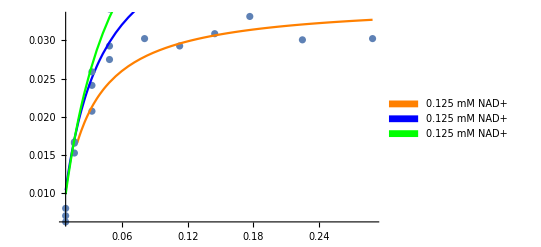

-Graphics-

Show[
Show[ListPlot[,PlotRang→{{-3,25},{-3,25}}],Plot[F[S],{S,-2,Max[icGAP]},PlotStyle→{{Orange,PointSize[Medium]}},Frame→True,PlotLegends→SwatchLegend[{Orange}, {0.125 mM NAD+}],PlotLabel→Style[    Ping-Pong Mechanism], AxesLabel→{ [1/GAP],(1/mM,1/Vo,(min/AU)},LabelStyle→Directive[14,Black]]]

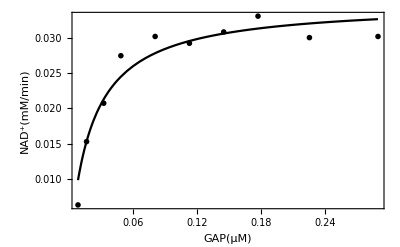

Kinetics_DATA1.png

```mathematica
PlotMM1=Show[ListPlot[Subscript[MMKinetics, data1],PlotTheme->"Monochrome",
PlotRange-> {{Min[QuantityMagnitude[Subscript[ℂ, data1mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data1mmol]]]},
{Min[QuantityMagnitude[Subscript[rxnVel, data1mmol]]],Max[QuantityMagnitude[Subscript[rxnVel, data1mmol]]]}},
Frame->True,FrameLabel->{{HoldForm[SuperPlus[NAD][mM/min]],None},{HoldForm[GAP[μM]],None}},
LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0]}],
Plot[{Subscript[nlmFit, data1][S]},{S,Min[QuantityMagnitude[Subscript[ℂ, data1mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data1mmol]]]},PlotRange-> {{Min[QuantityMagnitude[Subscript[ℂ, data1mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data1mmol]]]},
{Min[QuantityMagnitude[Subscript[rxnVel, data1mmol]]],Max[QuantityMagnitude[Subscript[rxnVel, data1mmol]]]}},PlotTheme->"Monochrome"]]
Export["Kinetics_DATA1.png",PlotMM]
```

```mathematica
Subscript[obsRate, data2]=QuantityArray[{0.050,0.104,0.150,0.182,0.237,0.241,0.264,0.259,0.266,0.232},"per minute"]
Subscript[Α, data2]={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800}
Subscript[ϵ, λ340]=Quantity[6220 ,1/("Centimeters"×"Molar")]
l=Quantity[1,"Centimeters"]
Subscript[ℂ, data2]=Subscript[Α, data2]/(Subscript[ϵ, λ340]×l)
Subscript[ℂ, data2mmol]=UnitConvert[Subscript[ℂ, data2],"Millimolar"]
Subscript[rxnVel, data2]=Subscript[obsRate, data2]/(Subscript[ϵ, λ340]×l)
Subscript[rxnVel, data2mmol]=UnitConvert[Subscript[rxnVel, data2],("Millimolar")/("Minutes")]
```

QuantityArray[…]

{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8}

6220 /(cm M)

1 cm

{8.03859×10^-6 M,0.0000160772 M,0.0000321543 M,0.0000482315 M,0.0000803859 M,0.00011254 M,0.000144695 M,0.000176849 M,0.00022508 M,0.000289389 M}

{0.00803859 mM,0.0160772 mM,0.0321543 mM,0.0482315 mM,0.0803859 mM,0.11254 mM,0.144695 mM,0.176849 mM,0.22508 mM,0.289389 mM}

QuantityArray[…]

QuantityArray[…]

```mathematica
Subscript[MMKinetics, data2]=Transpose[{QuantityMagnitude[Subscript[ℂ, data2mmol]],QuantityMagnitude[Subscript[rxnVel, data2mmol]]}]
Subscript[nlmFit, data2]=NonlinearModelFit[Subscript[MMKinetics, data2],(Subscript[V, MAX]×S)/(Subscript[κ, M]+S),{Subscript[V, MAX],Subscript[κ, M]},S]
Subscript[eqnMM, data2]=Normal[Subscript[nlmFit, data2]]

(* Statistics of Fit *)
Print["Statistics of Fit"]
Print["R^2 = ",Subscript[nlmFit, data2]["RSquared"]]
Print["Adjusted R^2 = ",Subscript[nlmFit, data2]["AdjustedRSquared"]]
Subscript[nlmFit, data2]["ParameterTable"]
Subscript[nlmFit, data2]["ParameterConfidenceIntervalTable"]
Subscript[paramtest, data2]=Subscript[nlmFit, data2]["BestFitParameters"]
Subscript[nlmFit, data2]["BestFit"]
```

{{0.00803859,0.00803859},{0.0160772,0.0167203},{0.0321543,0.0241158},{0.0482315,0.0292605},{0.0803859,0.0381029},{0.11254,0.038746},{0.144695,0.0424437},{0.176849,0.0416399},{0.22508,0.0427653},{0.289389,0.037299}}

FittedModel[(0.0474049 S)/(0.0285896+S)]

(0.0474049 S)/(0.0285896+S)

Statistics of Fit

R^2 = 0.994678

Adjusted R^2 = 0.993348

| Estimate | Standard Error | t-Statistic | P-Value
V_MAX | 0.0474049 | 0.00222349 | 21.32 | 2.46399×10^-8
κ_M | 0.0285896 | 0.00540845 | 5.28609 | 0.000740728

| Estimate | Standard Error | Confidence Interval
V_MAX | 0.0474049 | 0.00222349 | {0.0422775,0.0525323}
κ_M | 0.0285896 | 0.00540845 | {0.0161177,0.0410615}

{V_MAX→0.0474049,κ_M→0.0285896}

(0.0474049 S)/(0.0285896+S)

```mathematica
Print["V_max/κ_M = ",QuantityMagnitude[Subscript[V, MAX]/. Subscript[paramtest, data2]]/(Subscript[κ, M]/. Subscript[paramtest, data2])]
```

V_max/κ_M = 1.65812

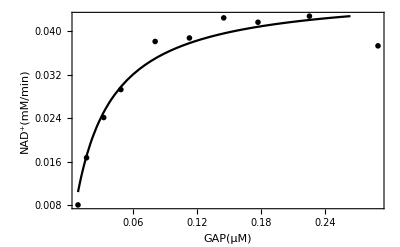

Kinetics_DATA2.png

```mathematica
PlotMM2=Show[ListPlot[Subscript[MMKinetics, data2],PlotTheme->"Monochrome",
PlotRange-> {{Min[QuantityMagnitude[Subscript[ℂ, data2mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data2mmol]]]},
{Min[QuantityMagnitude[Subscript[rxnVel, data2mmol]]],Max[QuantityMagnitude[Subscript[rxnVel, data2mmol]]]}},
Frame->True,FrameLabel->{{HoldForm[SuperPlus[NAD][mM/min]],None},{HoldForm[GAP[μM]],None}},
LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0]}],
Plot[{Subscript[nlmFit, data2][S]},{S,Min[QuantityMagnitude[Subscript[ℂ, data2mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data2mmol]]]},PlotRange-> {{Min[QuantityMagnitude[Subscript[ℂ, data2mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data2mmol]]]},
{Min[QuantityMagnitude[Subscript[rxnVel, data2mmol]]],Max[QuantityMagnitude[Subscript[rxnVel, data2mmol]]]}},PlotTheme->"Monochrome"]]
Export["Kinetics_DATA2.png",PlotMM]
```

```mathematica
Subscript[obsRate, data3]=QuantityArray[{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.310,0.334,0.322},"per minute"]
Subscript[Α, data]={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800}
Subscript[ϵ, λ340]=Quantity[6220 ,1/("Centimeters"×"Molar")]
l=Quantity[1,"Centimeters"]
Subscript[ℂ, data3]=Subscript[Α, data]/(Subscript[ϵ, λ340]×l)
Subscript[ℂ, data3mmol]=UnitConvert[Subscript[ℂ, data3],"Millimolar"]
Subscript[rxnVel, data3]=Subscript[obsRate, data3]/(Subscript[ϵ, λ340]×l)
Subscript[rxnVel, data3mmol]=UnitConvert[Subscript[rxnVel, data3],("Millimolar")/("Minutes")]
```

QuantityArray[…]

{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8}

6220 /(cm M)

1 cm

{8.03859×10^-6 M,0.0000160772 M,0.0000321543 M,0.0000482315 M,0.0000803859 M,0.00011254 M,0.000144695 M,0.000176849 M,0.00022508 M,0.000289389 M}

{0.00803859 mM,0.0160772 mM,0.0321543 mM,0.0482315 mM,0.0803859 mM,0.11254 mM,0.144695 mM,0.176849 mM,0.22508 mM,0.289389 mM}

QuantityArray[…]

QuantityArray[…]

```mathematica
Subscript[MMKinetics, data3]=Transpose[{QuantityMagnitude[Subscript[ℂ, data3mmol]],QuantityMagnitude[Subscript[rxnVel, data3mmol]]}]
Subscript[nlmFit, data3]=NonlinearModelFit[Subscript[MMKinetics, data3],(Subscript[V, MAX]×S)/(Subscript[κ, M]+S),{Subscript[V, MAX],Subscript[κ, M]},S]
Subscript[eqnMM, data3]=Normal[Subscript[nlmFit, data3]]

(* Statistics of Fit *)
Print["Statistics of Fit"]
Print["R^2 = ",Subscript[nlmFit, data3]["RSquared"]]
Print["Adjusted R^2 = ",Subscript[nlmFit, data3]["AdjustedRSquared"]]
Subscript[nlmFit, data3]["ParameterTable"]
Subscript[nlmFit, data3]["ParameterConfidenceIntervalTable"]
Subscript[paramtest, data3]=Subscript[nlmFit, data3]["BestFitParameters"]
Subscript[nlmFit, data3]["BestFit"]
```

{{0.00803859,0.00707395},{0.0160772,0.0165595},{0.0321543,0.0258842},{0.0482315,0.0340836},{0.0803859,0.0427653},{0.11254,0.0461415},{0.144695,0.0471061},{0.176849,0.0498392},{0.22508,0.0536977},{0.289389,0.0517685}}

FittedModel[(0.0621201 S)/(0.0425083+S)]

(0.0621201 S)/(0.0425083+S)

Statistics of Fit

R^2 = 0.998513

Adjusted R^2 = 0.998141

| Estimate | Standard Error | t-Statistic | P-Value
V_MAX | 0.0621201 | 0.0017663 | 35.1695 | 4.67527×10^-10
κ_M | 0.0425083 | 0.00417058 | 10.1924 | 7.36109×10^-6

| Estimate | Standard Error | Confidence Interval
V_MAX | 0.0621201 | 0.0017663 | {0.058047,0.0661932}
κ_M | 0.0425083 | 0.00417058 | {0.0328909,0.0521257}

{V_MAX→0.0621201,κ_M→0.0425083}

(0.0621201 S)/(0.0425083+S)

```mathematica
Print["V_max/κ_M = ",QuantityMagnitude[Subscript[V, MAX]/. Subscript[paramtest, data3]]/(Subscript[κ, M]/. Subscript[paramtest, data3])]
```

V_max/κ_M = 1.46136

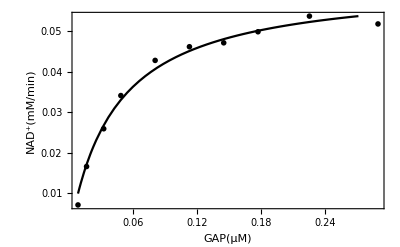

Kinetics_DATA3.png

```mathematica
PlotMM3=Show[ListPlot[Subscript[MMKinetics, data3],PlotTheme->"Monochrome",
PlotRange-> {{Min[QuantityMagnitude[Subscript[ℂ, data3mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data3mmol]]]},
{Min[QuantityMagnitude[Subscript[rxnVel, data3mmol]]],Max[QuantityMagnitude[Subscript[rxnVel, data3mmol]]]}},
Frame->True,FrameLabel->{{HoldForm[SuperPlus[NAD][mM/min]],None},{HoldForm[GAP[μM]],None}},
LabelStyle->{FontFamily->"Helvetica",12,GrayLevel[0]}],
Plot[{Subscript[nlmFit, data3][S]},{S,Min[QuantityMagnitude[Subscript[ℂ, data3mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data3mmol]]]},PlotRange-> {{Min[QuantityMagnitude[Subscript[ℂ, data3mmol]]],Max[QuantityMagnitude[Subscript[ℂ, data3mmol]]]},
{Min[QuantityMagnitude[Subscript[rxnVel, data3mmol]]],Max[QuantityMagnitude[Subscript[rxnVel, data3mmol]]]}},PlotTheme->"Monochrome"]]
Export["Kinetics_DATA3.png",PlotMM]
```